```mathematica
ClearAll["Global`*"]
```

```mathematica
Needs["ErrorBarPlots`"]
```

# Multiple Files

## Input

```mathematica
fileList = {{"210608", "021"}, {"210608", "022"}, {"210608", "023"}, {"210608", "024"}, {"210608", "025"}, {"210608", "026"}, {"210608", "028"}};
timeData = {0,25,50,100,150,200, 250}; 
Nruns = 200;
```

## Analysis

```mathematica
SetDirectory["C:\\Users\\labadmin\\Documents\\Jarvis\\data\\"];

getProbs[filedata_] := 
Mean[Import[filedata⟦1⟧<>"\\"<>filedata⟦2⟧<>"_PROB_"<>filedata⟦1⟧<>".csv"]⟦2⟧]/100
```

```mathematica
probList = Map[getProbs, fileList];
lifetimedataplot= Table[{{timeData⟦i⟧, probList⟦i⟧}, ErrorBar[Sqrt[(Abs[probList⟦i⟧ - (1 - probList⟦i⟧)])/Nruns]]}, {i, 1, Length[probList]}];
```

## Fit

```mathematica
decayfunc[tvar_, Γ_] :=2/3 Exp[-tvar/Γ] + 1/3;
decayfit = NonlinearModelFit[Transpose[{timeData,  probList}],decayfunc[tvar, Γ],{{Γ,350}},tvar];
```

| Estimate | Standard Error | t-Statistic | P-Value
Γ | 573.051 | 97.1999 | 5.89559 | 0.00105738

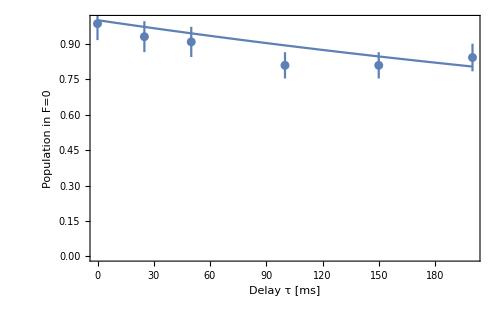

```mathematica
decayfit["ParameterTable"]
Show[ErrorListPlot[lifetimedataplot],
Plot[decayfit["BestFit"]/.tvar-> t, {t, 0, 200}],
PlotRange-> {{0, 200},{0,1}},
Frame-> True, ImageSize-> 500, AxesOrigin-> False,FrameLabel->{{"Population in F=0",Null},{"Delay τ [ms]",Null}}, FrameStyle-> {Black, Bold}, LabelStyle-> {15}]
```

# Single File

## Input

```mathematica
file = {"200923", "041"};
timestep = 25;
Nruns = 100;
```

## Analysis

```mathematica
SetDirectory["C:\\Users\\labadmin\\Documents\\Jarvis\\data\\"];

getProbs[filedata_] := 
Import[filedata⟦1⟧<>"\\"<>filedata⟦2⟧<>"_PROB_"<>filedata⟦1⟧<>".csv"]⟦2⟧
```

```mathematica
probList = getProbs[ file]/100;
timeData = Table[i  timestep , {i, 0, Length[probList] - 1}];
```

```mathematica
lifetimedataplot= Table[{{timeData⟦i⟧, 
probList⟦i⟧}, ErrorBar[Sqrt[(Abs[probList⟦i⟧ - (1 - probList⟦i⟧)])/Nruns]]}, {i, 1, Length[probList]}];
```

## Fit

```mathematica
decayfunc[tvar_, Γ_] :=2/3 Exp[-tvar/Γ] + 1/3;
decayfit = NonlinearModelFit[Transpose[{timeData,  probList}],decayfunc[tvar, Γ],{{Γ,350}},tvar];
```

| Estimate | Standard Error | t-Statistic | P-Value
Γ | 721.829 | 194.626 | 3.7088 | 0.0138721

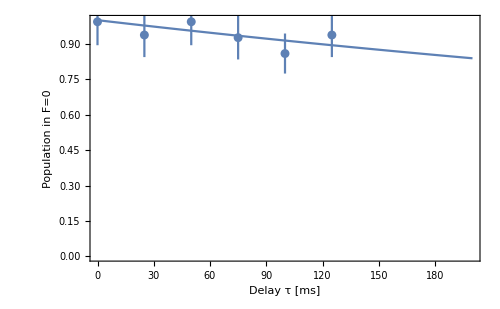

```mathematica
decayfit["ParameterTable"]
Show[ErrorListPlot[lifetimedataplot],
Plot[decayfit["BestFit"]/.tvar-> t, {t, 0, 200}],
PlotRange-> {{0, 200},{0,1}},
Frame-> True, ImageSize-> 500, AxesOrigin-> False,FrameLabel->{{"Population in F=0",Null},{"Delay τ [ms]",Null}}, FrameStyle-> {Black, Bold}, LabelStyle-> {15}]
```